```mathematica
repsim=Block[{v="A"}, Table[With[{res=Symbol[v<>ToString[k]]->Symbol[ToLowerCase[v]]},v=NextLetter[v];res],{k,9}]]
```

{A1→a,B2→b,C3→c,D4→d,E5→e,F6→f,G7→g,H8→h,I9→i}

```mathematica
(CalculateInOutFormulaMany[CompleteGraph[3],Table[{k},{k,3}],"A"]//Factor)/.repsim
```

(-2+a) (-1+b) c

```mathematica
(CalculateInOutFormulaMany[CompleteGraph[6],Table[{k},{k,6}],"A"]//Factor)/.repsim
```

(-5+a) (-4+b) (-3+c) (-2+d) (-1+e) f

```mathematica
Test[a_]:=Print[a]
```

```mathematica
Test[True]
```

True

```mathematica
(CalculateInOutFormulaMany[CycleGraph[6],Table[{k},{k,6}],"A"]//Factor)/.repsim
```

(5-a-2 b+a b-3 c+a c+2 b c-a b c-4 d+a d+2 b d-a b d+3 c d-a c d-2 b c d+a b c d) (-1+e) f

```mathematica
(CalculateInOutFormulaMany[CycleGraph[5],Table[{k},{k,5}],"A"]//Factor)/.repsim
```

(-4+a+2 b-a b+3 c-a c-2 b c+a b c) (-1+d) e

```mathematica
Block[{v="A"}, Table[With[{res=Symbol[v<>ToString[k]]},v=NextLetter[v];res->x],{k,10}]]
```

{A1→x,B2→x,C3→x,D4→x,E5→x,F6→x,G7→x,H8→x,I9→x,J10→x}

```mathematica
(-4+A1+2 B2-A1 B2+3 C3-A1 C3-2 B2 C3+A1 B2 C3) (-1+D4) E5/.{A1->x,B2->x,C3->x,D4->x,E5->x,F6->x,G7->x,H8->x,I9->x,J10->x}
```

(-1+x) x (-4+6 x-4 x^2+x^3)

```mathematica
((5-A1-2 B2+A1 B2-3 C3+A1 C3+2 B2 C3-A1 B2 C3-4 D4+A1 D4+2 B2 D4-A1 B2 D4+3 C3 D4-A1 C3 D4-2 B2 C3 D4+A1 B2 C3 D4) (-1+E5) F6)/.{A1->x,B2->x,C3->x,D4->x,E5->x,F6->x,G7->x,H8->x,I9->x,J10->x}
```

(-1+x) x (5-10 x+10 x^2-5 x^3+x^4)

```mathematica
(With[{kk=6},CalculateInOutFormulaMany[CycleGraph[kk],Table[{k},{k,kk}],"A"]//Factor])/.repsim
```

(5-a-2 b+a b-3 c+a c+2 b c-a b c-4 d+a d+2 b d-a b d+3 c d-a c d-2 b c d+a b c d) (-1+e) f

```mathematica
(5-A1-2 B2+A1 B2-3 C3+A1 C3+2 B2 C3-A1 B2 C3-4 D4+A1 D4+2 B2 D4-A1 B2 D4+3 C3 D4-A1 C3 D4-2 B2 C3 D4+A1 B2 C3 D4) (-1+E5) F6/.{A1->y,B2->z,C3->x,D4->a,E5->x,F6->x,G7->x,H8->x,I9->x,J10->x}
```

(-1+x) x (5-4 a-3 x+3 a x-y+a y+x y-a x y-2 z+2 a z+2 x z-2 a x z+y z-a y z-x y z+a x y z)

```mathematica
SymmetricPolynomial[3,{a,x,y,z}]//Factor
```

a x y+a x z+a y z+x y z

```mathematica
(With[{kk=6},CalculateInOutFormulaMany[WheelGraph[kk],Table[{k},{k,kk}],"A"]//Factor])/.repsim
```

(30-4 a-9 b+a b-15 c+2 a c+6 b c-a b c-21 d+3 a d+7 b d-a b d+12 c d-2 a c d-5 b c d+a b c d) (-1+e) f

```mathematica
EdgeList[WheelGraph[6]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->6,3<->4,4<->5,5<->6}

```mathematica
With[{kk=6},CalculateInOutFormulaMany[EdgeDelete[WheelGraph[kk],5<->6],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(-16+a+4 b+6 c-2 b c+7 d-2 b d-3 c d+b c d+30 e-4 a e-9 b e+a b e-15 c e+2 a c e+6 b c e-a b c e-21 d e+3 a d e+7 b d e-a b d e+12 c d e-2 a c d e-5 b c d e+a b c d e) f

```mathematica
With[{kk=6},CalculateInOutFormulaMany[EdgeDelete[WheelGraph[kk],1<->6],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(22-4 a-5 b+a b-11 c+2 a c+4 b c-a b c-17 d+3 a d+5 b d-a b d+10 c d-2 a c d-4 b c d+a b c d) (-1+e) f

```mathematica
move16=(22-4 a-5 b+a b-11 c+2 a c+4 b c-a b c-17 d+3 a d+5 b d-a b d+10 c d-2 a c d-4 b c d+a b c d) (-1+e) f
```

(22-4 a-5 b+a b-11 c+2 a c+4 b c-a b c-17 d+3 a d+5 b d-a b d+10 c d-2 a c d-4 b c d+a b c d) (-1+e) f

```mathematica
wheel6=With[{kk=6},CalculateInOutFormulaMany[WheelGraph[kk],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(30-4 a-9 b+a b-15 c+2 a c+6 b c-a b c-21 d+3 a d+7 b d-a b d+12 c d-2 a c d-5 b c d+a b c d) (-1+e) f

```mathematica
move16-wheel6//Simplify
```

(-2+b) (-2+c) (-2+d) (-1+e) f

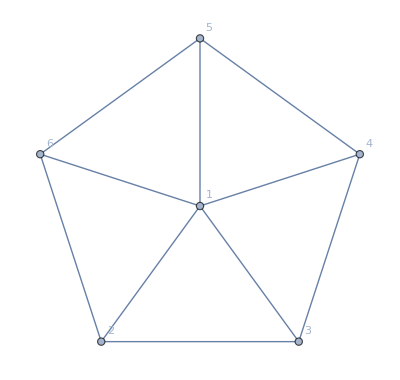

```mathematica
WheelGraph[6,VertexLabels->"Name"]
```

```mathematica
contract16=With[{kk=6},CalculateInOutFormulaMany[EdgeContract[WheelGraph[kk],6<->1],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(-8+a+5 b-a b+6 c-a c-4 b c+a b c) (-1+d) e

```mathematica
move56=With[{kk=6},CalculateInOutFormulaMany[EdgeDelete[WheelGraph[kk],5<->6],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(-16+a+4 b+6 c-2 b c+7 d-2 b d-3 c d+b c d+30 e-4 a e-9 b e+a b e-15 c e+2 a c e+6 b c e-a b c e-21 d e+3 a d e+7 b d e-a b d e+12 c d e-2 a c d e-5 b c d e+a b c d e) f

```mathematica
contract56=With[{kk=6},CalculateInOutFormulaMany[EdgeContract[WheelGraph[kk],5<->6],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(-14+3 a+5 b-a b+9 c-2 a c-4 b c+a b c) (-1+d) e

```mathematica
(move56-wheel6//Simplify)/.f->e
```

(-14+b (5-4 c)+a (3+b (-1+c)-2 c)+9 c) (-1+d) e

```mathematica
Simplify[contract56]
```

(-14+b (5-4 c)+a (3+b (-1+c)-2 c)+9 c) (-1+d) e

```mathematica
move12=With[{kk=6},CalculateInOutFormulaMany[EdgeDelete[WheelGraph[kk],1<->2],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(22-4 a-8 b+a b-10 c+2 a c+5 b c-a b c-15 d+3 a d+6 b d-a b d+8 c d-2 a c d-4 b c d+a b c d) (-1+e) f

```mathematica
contract12=With[{kk=6},CalculateInOutFormulaMany[EdgeContract[WheelGraph[kk],1<->2],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(-8+a+5 c-a c+6 d-a d-4 c d+a c d) (-1+e) f

```mathematica
((move12-wheel6//Simplify)//Factor)/.b->a
```

(-8+a+5 c-a c+6 d-a d-4 c d+a c d) (-1+e) f

```mathematica
With[{kk=3},CalculateInOutFormulaMany[CompleteGraph[kk],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(-2+a) (-1+b) c

```mathematica
With[{kk=3},CalculateInOutFormulaMany[EdgeDelete[CompleteGraph[kk],1<->2],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(-1+a) (-1+b) c

```mathematica
With[{kk=3},CalculateInOutFormulaMany[EdgeDelete[EdgeDelete[CompleteGraph[kk],1<->2],1<->3],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

a (-1+b) c

```mathematica
With[{kk=6},CalculateInOutFormulaMany[EdgeDelete[CompleteGraph[kk],1<->2],Table[{k},{k,kk}],"A"]//Factor]/.repsim
```

(-4+a) (-4+b) (-3+c) (-2+d) (-1+e) f

```mathematica
TableForm[Table[Factor[CalculateInOutFormulaMany[CycleGraph[kk],Table[{k},{k,kk}],"A"]]/.repsim,{kk,3,7}]]
```

(-2+a) (-1+b) c
(3-a-2 b+a b) (-1+c) d
(-4+a+2 b-a b+3 c-a c-2 b c+a b c) (-1+d) e
(5-a-2 b+a b-3 c+a c+2 b c-a b c-4 d+a d+2 b d-a b d+3 c d-a c d-2 b c d+a b c d) (-1+e) f
(-6+a+2 b-a b+3 c-a c-2 b c+a b c+4 d-a d-2 b d+a b d-3 c d+a c d+2 b c d-a b c d+5 e-a e-2 b e+a b e-3 c e+a c e+2 b c e-a b c e-4 d e+a d e+2 b d e-a b d e+3 c d e-a c d e-2 b c d e+a b c d e) (-1+f) g

```mathematica
TableForm[Table[Factor[ChromaticPolynomial[CycleGraph[kk],x]],{kk,3,7}]]
```

(-2+x) (-1+x) x
(-1+x) x (3-3 x+x^2)
(-2+x) (-1+x) x (2-2 x+x^2)
(-1+x) x (5-10 x+10 x^2-5 x^3+x^4)
(-2+x) (-1+x) x (3-3 x+x^2) (1-x+x^2)

```mathematica
TableForm[Table[Factor[ChromaticPolynomial[CycleGraph[kk],2]],{kk,3,7}]]
```

0
2
0
2
0